c-a ⅇ^(-b (-T+x))

ConditionalExpression[-(-b T-Log[a/(c-y)])/b,(a>0&&y<c)||(a<0&&y>c)]

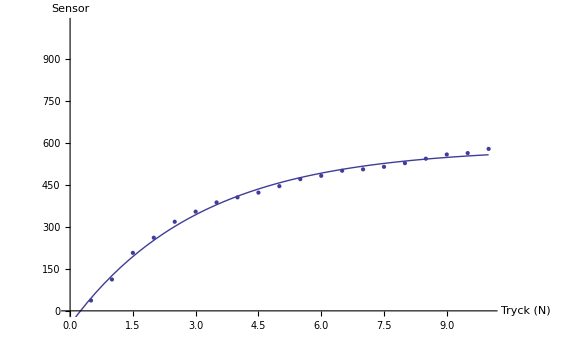
{ConditionalExpression[-3.08873 (-1.17474-Log[194.768/(581.77-y)]),y<581.77],-Graphics-}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

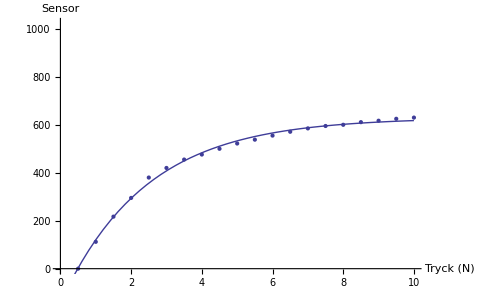
{ConditionalExpression[-2.40577 (-1.16244-Log[241.382/(629.651-y)]),y<629.651],-Graphics-}

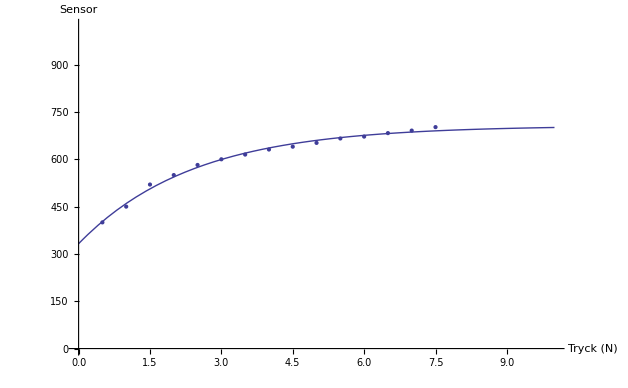
{ConditionalExpression[-2.40101 (-0.982137-Log[140.161/(706.628-y)]),y<706.628],-Graphics-}

```mathematica
ClearAll["Gloabl`*"]
pekfinger={{0.5,400},{1,450},{1.5,520},{2,550},{2.5,582},{3,600},{3.5,615},{4,631},{4.5,640},{5,652},{5.5,666},{6,672},{6.5,683},{7,691},{7.5,702}};

langfinger={{0.5,37},{1,112},{1.5,207},{2,261},{2.5,318},{3,354},{3.5,387},{4,405},{4.5,422},{5,445},{5.5,470},{6,482},{6.5,500},{7,505},{7.5,514},{8,527},{8.5,543},{9,558},{9.5,563},{10,578}};
tumme={{0.5,0},{1,112},{1.5,217},{2,295},{2.5,380},{3,420},{3.5,455},{4,476},{4.5,500},{5,522},{5.5,538},{6,555},{6.5,571},{7,585},{7.5,595},{8,600},{8.5,611},{9,617},{9.5,625},{10,630}};

f=-a Exp[-b (x-T)]+c
(*Inverse*)
finv = x/.Solve[y == f, x, Reals][[1,1]]
(*lista = langfinger;
Manipulate[
p0 = ListPlot[lista];
p1 = Plot[-a Exp[-b (x-T)]+c, {x, 0, 10}];
Show[p0, p1, AxesOrigin->{0,0}, PlotRange->{-1023, 1023}, AxesLabel->{"Tryck (N)", "Sensor"}]
,{a, 0, 1000}, {b, 0, 2}, {c, 0, 1000}, {T, 0, 10}]*)

mkgraph[lista_] := Block[{func, p0, p1},
vals = FindFit[lista, f, {{a, 218}, {b, 0.47},{c, 558}, {T, 2.58}}, x, MaxIterations->10000];
p0 = ListPlot[lista];
p1 = Plot[f/. vals, {x, 0, 10}];
{finv /. vals, Show[p0, p1, AxesOrigin->{0,0}, PlotRange->{0, 1023}, AxesLabel->{"Tryck (N)", "Sensor"}]}
]


mkgraph[langfinger]
mkgraph[tumme]
mkgraph[pekfinger]
```